#### BC_DirectPath_supp_5.nb Run common_funs, ES_FindSymGroups, ChooseTmat, BC_DirectPath This will work for two different versions (see BC_DirectPath): 1) t1 = 0, t2 = 1, dt = 0.05 [ZoomIn = False] 2) t1 = 0.8, t2 = 0.9, dt = 0.01 [ZoomIn = True] The triangle minimum is very close to 0.85

```mathematica
SigCurve=XISO;
nm=nm1;
```

```mathematica
Tmat1==TTET
Tmat2==TCUBE
```

```mathematica
If[t2==0.9,ZoomIn=True,ZoomIn=False]
```

```mathematica
AddPeak=False;  (* since the triangle peak at 0.85 is a discretization point, we do not need to add it to the plot *)
```

#### Display data from TrivPathToISO.

```mathematica
MatrixForm[Tmat1]
MatrixForm[Chop[Tmat2,0.0001]]
MatrixForm[UforNM1]
```

```mathematica
dt
```

#### Round is necessary for Mathematica to recognize, for example, that 0.25 + 0.05 = 0.3

```mathematica
slope[t_]:=((βT[TT[Round[t+dt,dt],Tmat1,Tmat2],SigCurve]-βT[TT[t,Tmat1,Tmat2],SigCurve])/Degree)/dt;
```

#### Slope of each segment

```mathematica
MatrixNote[Tmat]
Ranget
dt
TableForm[Join[{{"Index","   t","  βTET","  slope"}},MapIndexed[{First[#2],PaddedForm[#[[1]],{2,2}],PaddedForm[Round[#[[2]]/Degree,.001],{4,3}],PaddedForm[#[[3]],{5,2}]}&,Transpose[{Ranget,βT[TT[#,Tmat1,Tmat2],SigCurve]&/@Ranget,slope/@Ranget}]]]]
```

#### Find the intersection between t = tt1 and t = tt2 (review the slope values listed above)

```mathematica
If[ZoomIn,{ipick1=3;ipick2=8;},{ipick1=16;ipick2=20;}];
tt1=Ranget[[ipick1]]
tt2=Ranget[[ipick2]]
slope[tt1]
slope[tt2]
beta1=βT[TT[tt1,Tmat1,Tmat2],SigCurve]/Degree
beta2=βT[TT[tt2,Tmat1,Tmat2],SigCurve]/Degree
```

```mathematica
peak=({t,beta}/.Solve[(beta-beta1)/(t-tt1)==slope[tt1]&&(beta-beta2)/(t-tt2)==slope[tt2],{t,beta}])[[1]]
```

```mathematica
(* If[ZoomIn,peak={0.85,0}] *)
```

```mathematica
Bcurve[AddPeak_]:=If[AddPeak,Sort[Join[{peak},{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}&/@Ranget]],{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}&/@Ranget]
```

```mathematica
Length[Bcurve[False]]
Length[Bcurve[True]]
```

```mathematica
MatrixNote[Tmat]
Ranget
dt
plot=Graphics[{PointSize[.015],
Line[Bcurve[AddPeak]],
{ColorData["Rainbow"][0/6],Point[{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}]&/@Ranget},
Point[{#,0}]&/@Ranget},Axes->True,AxesOrigin->{t1,0},AspectRatio->.5,ImageSize->500,Ticks->{Range[0,1,.2],Automatic},TicksStyle->14]
```

#### pick subset of balls original zoom: 1,3,5,6,9,11 final zoom: 3,4,5,6,7,8

```mathematica
Ranget
If[ZoomIn,ipick={3,4,5,6,7,8};,ipick={1,5,9,13,17,21};]
ipick
Ranget[[ipick]]
```

```mathematica
tleft=Ranget[[First[ipick]]]
tright=Ranget[[Last[ipick]]]
Tleft=TT[tleft,Tmat1,Tmat2];
Tright=TT[tright,Tmat1,Tmat2];
```

#### Determine the color scale for the subset of maps to plot

```mathematica
npts =10000;
AlphaMONOvalues=Sort[Table[Alpha[Tleft,{RandomReal[{-π,π}],RandomReal[{0,π}]},MONO]/Degree,{k,npts}]];
Take[AlphaMONOvalues,5]
Take[AlphaMONOvalues,-5]
AlphaMONOvalues=Sort[Table[Alpha[Tright,{RandomReal[{-π,π}],RandomReal[{0,π}]},MONO]/Degree,{k,npts}]];
Take[AlphaMONOvalues,5]
Take[AlphaMONOvalues,-5]
```

```mathematica
If[ZoomIn,{cmin=0;cmax=6; dc=0.5;},{cmin=0;cmax=25; dc=1;}];
contours=Range[cmin,cmax,dc]
MaxForScaling=cmax-dc
```

```mathematica
eye=20xyztp[{30,65}];
AngRad=.05;
ShiftToEye=.02;
tkns=.01;  (* tkns only affects XISO *)
```

#### Basic output for the ball plots

```mathematica
MatrixNote[Tmat]
contours
MaxForScaling
PrintEye;
```

#### Because this is a subset nm1 path, we already have the U, and it will be identical for TET balls on the bottom.

```mathematica
TwoFoldSig1=Graphics3D[TwoFoldGraphics[Sig1,UforNM1,1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]];
TwoFoldSig2=Graphics3D[TwoFoldGraphics[Sig2,UforNM1,1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]];
TwoFoldSigCurve=Graphics3D[TwoFoldGraphics[SigCurve,UforNM1,1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]];
```

#### left ball on bottom

```mathematica
(*tIs0=Show[{cpMONO[Tmat1,contours,MaxForScaling, plotpoints, contourstyle],TwoFoldBottom},options]*)
```

```mathematica
tIsPt1onBottom=Show[{cpMONO[Tleft,contours,MaxForScaling, plotpoints, contourstyle],TwoFoldSig1},options]
```

```mathematica
tIsPt2onBottom=Show[{cpMONO[TT[Ranget[[ipick[[2]]]],Tmat1,Tmat2],contours,MaxForScaling, plotpoints, contourstyle],TwoFoldSig1},options];
tIsPt3onBottom=Show[{cpMONO[TT[Ranget[[ipick[[3]]]],Tmat1,Tmat2],contours,MaxForScaling, plotpoints, contourstyle],TwoFoldSig1},options];
If[ZoomIn,tIsPt4onBottom=Show[{cpMONO[TT[Ranget[[ipick[[4]]]],Tmat1,Tmat2],contours,MaxForScaling, plotpoints, contourstyle],TwoFoldSigCurve},options],
tIsPt4onBottom=Show[{cpMONO[TT[Ranget[[ipick[[4]]]],Tmat1,Tmat2],contours,MaxForScaling, plotpoints, contourstyle],TwoFoldSig1},options]];
tIsPt5onBottom=Show[{cpMONO[TT[Ranget[[ipick[[5]]]],Tmat1,Tmat2],contours,MaxForScaling, plotpoints, contourstyle],TwoFoldSig1},options];
```

#### right ball on bottom

```mathematica
If[ZoomIn,TwoFoldRightBottom=TwoFoldSig1, TwoFoldRightBottom=TwoFoldSig2];
tIsPt6onBottom=Show[{cpMONO[TT[Ranget[[ipick[[6]]]],Tmat1,Tmat2],contours,MaxForScaling, plotpoints, contourstyle],TwoFoldRightBottom},options]
```

#### Demonstrate an issue related to how Mathematica is storing values.

```mathematica
(* MatrixForm[Chop[Closest[TT[#,Tmat1,Tmat2],SigCurve],0.001]]&/@Ranget *)
```

```mathematica
(* MatrixForm[Chop[UT[TT[#,Tmat1,Tmat2],SigCurve],0.001]]&/@Ranget *)
```

```mathematica
If[Not[ZoomIn],
{Ranget[[7]],
Ranget[[7]]==.3,
βT[TT[Ranget[[7]],Tmat1,Tmat2],SigCurve],
βT[TT[.3,Tmat1,Tmat2],SigCurve],
βT[TT[Ranget[[7]],Tmat1,Tmat2],SigCurve]==βT[TT[.3,Tmat1,Tmat2],SigCurve]}]
```

```mathematica
If[Not[ZoomIn],
{Ranget[[13]],
Ranget[[13]]==.6,
βT[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve],
βT[TT[.6,Tmat1,Tmat2],SigCurve],
βT[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve]==βT[TT[.6,Tmat1,Tmat2],SigCurve]}]
```

#### Balls on the top of the triangle

```mathematica
MatrixNote[Tmat]
contours
MaxForScaling
PrintEye;
```

#### left ball on top

```mathematica
(* tIsPt1onTop=Show[{cpMONO[Closest[Tmat1,SigCurve],contours,MaxForScaling, plotpoints, contourstyle],
Graphics3D[TwoFoldGraphics[SigCurve,UT[Tmat1,SigCurve],1.25AngRadDisk,3ShiftToEye,eye,tkns,Green]]},options] *)
```

```mathematica
tIsPt1onTop=Show[{cpMONO[Closest[Tleft,SigCurve],contours,MaxForScaling, plotpoints, contourstyle],TwoFoldSigCurve},options]
```

```mathematica
tIsPt2onTop=Show[{cpMONO[Closest[TT[Ranget[[ipick[[2]]]],Tmat1,Tmat2],SigCurve],contours,MaxForScaling, plotpoints, contourstyle],TwoFoldSigCurve},options];
tIsPt3onTop=Show[{cpMONO[Closest[TT[Ranget[[ipick[[3]]]],Tmat1,Tmat2],SigCurve],contours,MaxForScaling, plotpoints, contourstyle],TwoFoldSigCurve},options];
tIsPt4onTop=Show[{cpMONO[Closest[TT[Ranget[[ipick[[4]]]],Tmat1,Tmat2],SigCurve],contours,MaxForScaling, plotpoints, contourstyle],TwoFoldSigCurve},options];
tIsPt5onTop=Show[{cpMONO[Closest[TT[Ranget[[ipick[[5]]]],Tmat1,Tmat2],SigCurve],contours,MaxForScaling, plotpoints, contourstyle],TwoFoldSigCurve},options];
```

#### right ball on top

```mathematica
tIsPt6onTop=Show[{cpMONO[Closest[TT[Ranget[[ipick[[6]]]],Tmat1,Tmat2],SigCurve],contours,MaxForScaling, plotpoints, contourstyle],TwoFoldSigCurve},options]
```

#### MAIN PLOT

```mathematica
(*Ranget[[13]]
βT[TT[0.6,Tmat1,Tmat2],SigCurve]/Degree
βT[TT[Ranget[[13]],Tmat1,Tmat2],SigCurve]/Degree *)
```

```mathematica
MatrixNote[Tmat]
Ranget
contours
MaxForScaling
PrintEye;

dxran = tright-tleft;
bsize=0.18;
aspectratio=0.5;
dytop=10;
dyTmat=30;
dySig=-20;
x0=0.2;
(* If[ZoomIn,{bsize=0.018;dyTmat=2.5;dySig=-2.;dytop=1;x0=0;}]; *)
If[ZoomIn,{bsize=0.009;dyTmat=2.5;dySig=-2.;dytop=1;x0=0;}]; 

dybot=-dytop;
dyvertline=dytop;
dxlabs=x0+{0.3,0.52,0.7};
dxTmat=tleft+dxlabs[[1]]dxran;
dxnm = tleft+dxlabs[[2]]dxran;
dynm=dyTmat;
dxU = tleft+dxlabs[[3]]dxran;
dyU=dyTmat;

Graphics[{PointSize[.013],
(*{PointSize[.001],Point/@{{.1,-14.0},{.5,20.0}}},   (* fake points *) *)
(* conector lines on bottom *)
Line[{{Ranget[[#]],0},{Ranget[[#]],-dyvertline}}]&/@ipick,
(* connector lines on top *)
Line[{{Ranget[[#]],                           βT[TT[Ranget[[#]],Tmat1,Tmat2],SigCurve]/Degree},
    {Ranget[[#]],dyvertline+βT[TT[Ranget[[#]],Tmat1,Tmat2],SigCurve]/Degree}}]&/@ipick,
Line[{{tleft,0},{tleft,βT[Tleft,SigCurve]/Degree}}], (* left side line *)
Line[{{tright,0},{tright,βT[Tright,SigCurve]/Degree}}], (* right side line *)
(* main triangle lines *)
{HueOfΣ[SigCurve],Line[Sort[Join[{peak},{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}&/@Ranget[[ipick]]]]]},
{HueOfΣ[SigCurve],Point[{#,βT[TT[#,Tmat1,Tmat2],SigCurve]/Degree}]&/@Ranget[[ipick]]},
(* text labels for coordinates of left and right base points *)
Text[Style[SequenceForm["(",tleft,", 0)"],16],{tleft-0.02dxran,0},{1,0}],
Text[Style[SequenceForm["(",tright,", 0)"],16],{tright+0.02dxran,0},{-1,0}],
Inset[tIsPt1onTop,{Ranget[[ipick[[1]]]],dytop+βT[TT[Ranget[[ipick[[1]]]],Tmat1,Tmat2],SigCurve]/Degree},Center,bsize],
Inset[tIsPt2onTop,{Ranget[[ipick[[2]]]],dytop+βT[TT[Ranget[[ipick[[2]]]],Tmat1,Tmat2],SigCurve]/Degree},Center,bsize],
Inset[tIsPt3onTop,{Ranget[[ipick[[3]]]],dytop+βT[TT[Ranget[[ipick[[3]]]],Tmat1,Tmat2],SigCurve]/Degree},Center,bsize],
Inset[tIsPt4onTop,{Ranget[[ipick[[4]]]],dytop+βT[TT[Ranget[[ipick[[4]]]],Tmat1,Tmat2],SigCurve]/Degree},Center,bsize],
Inset[tIsPt5onTop,{Ranget[[ipick[[5]]]],dytop+βT[TT[Ranget[[ipick[[5]]]],Tmat1,Tmat2],SigCurve]/Degree},Center,bsize],
Inset[tIsPt6onTop,{Ranget[[ipick[[6]]]],dytop+βT[TT[Ranget[[ipick[[6]]]],Tmat1,Tmat2],SigCurve]/Degree},Center,bsize],
Inset[tIsPt1onBottom,{Ranget[[ipick[[1]]]],dybot},Center,bsize],
Inset[tIsPt2onBottom,{Ranget[[ipick[[2]]]],dybot},Center,bsize],
Inset[tIsPt3onBottom,{Ranget[[ipick[[3]]]],dybot},Center,bsize],
Inset[tIsPt4onBottom,{Ranget[[ipick[[4]]]],dybot},Center,bsize],
Inset[tIsPt5onBottom,{Ranget[[ipick[[5]]]],dybot},Center,bsize],
Inset[tIsPt6onBottom,{Ranget[[ipick[[6]]]],dybot},Center,bsize],
(*Inset[tIs0,{0,dybot},Center,bsize],*)
(*Inset[tIs1,{1,dybot},Center,bsize],*)
(* TRIV base curve *)
{HueOfΣ[TRIV],Line[{{tleft,0},{tright,0}}]},
{HueOfΣ[TRIV],Point[{#,0}]&/@Ranget[[ipick]]},
 (* betaΣ for nm2, like Subscript[β, XISO]^ (15.98) *)
Text[Style[SequenceForm[BetaText[SigCurve]," (",Round[βT[Tleft,SigCurve]/Degree,0.01],"°)"],16,FontColor->HueOfΣ[SigCurve] ],{tleft-0.02 dxran,βT[Tleft,SigCurve]/Degree},{1,0}],
(* Sigma labels *)
Text[Style[Sig1,16],{tleft,dySig}],
If[Not[ZoomIn],Text[Style[Sig2,16],{tright,dySig}]],
 (* Tmat text label *)
Text[Framed[Style[MatrixNote[Tmat],16],Background->White,FrameStyle->Black,FrameMargins->Medium ],
{dxTmat,dyTmat},{-1,0}],
 (* nm text label *)
Text[Framed[Style[SequenceForm["node mode is ",TextNM[nm]],12],Background->White,FrameStyle->Black,FrameMargins->Small ],
{dxnm,dynm},{1,0}],
(* U for nm1 *)
If[nm===nm1,Text[SequenceForm[Style["U",{16,Italic}],Style[" = ",16],Style[DispMat[UforNM1,2],10] ],{dxU,dyU},{1,0}]] 
},Axes->False,AspectRatio->aspectratio,ImageSize->1000,PlotRange->All]
```

## Igel dt = 0.05, Tmat1=TTET, Tmat2=TCUBE, ListSigma = {XISO}, nm1 with UforNM1 = UXISO [supp5]

#### From BC_Superlattice.nb (dt = 0.2)

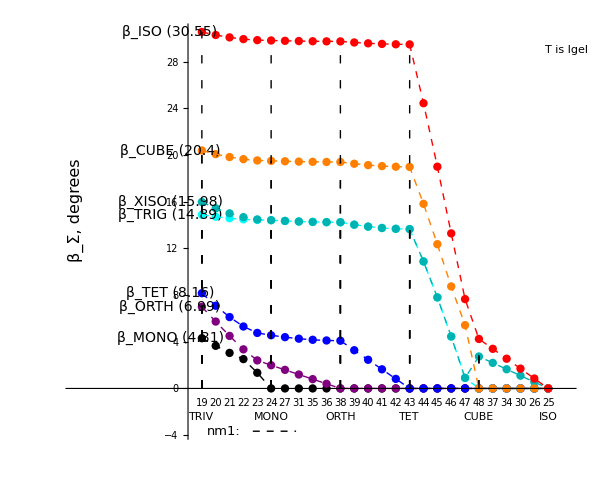

#### From BC_DirectPath.nb